# The Art of Elementary Cellular Automata

```mathematica
Panel[Style[RulePlot[CellularAutomaton[30], {{1},0},50, PlotLegends->"Icon", Appearance->"Contiguous"], Magnification->0.75], "Rule 30", Bottom, Appearance->"Frameless"]
```

-Graphics-Rule 30

## CA Specification Format

Each CA rule is a function from bit-triples to bits; b^3→b, where b = {0,1}. This is typically expressed with a bit string, from which the wolfram number of that CA is derived, as follows:

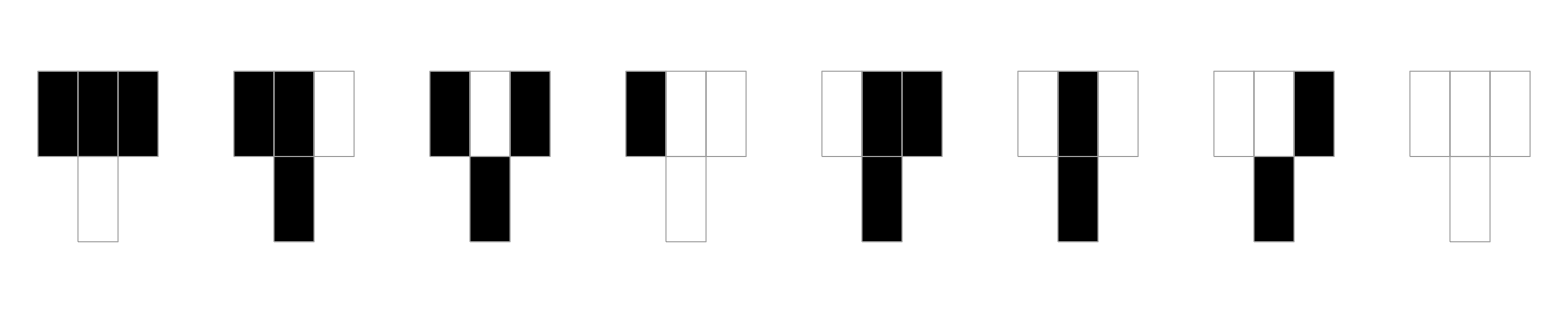

```mathematica
RulePlot[CellularAutomaton["Rule110"], PlotLegends->"Text", Appearance->"Contiguous", Frame->False]
```

The rule number 110 is derived by reading the bit string as a single 8-bit integer. However,

## Miscellaneous

```mathematica
Speak[b^3->b]
```

```mathematica
RulePlot[CellularAutomaton[110], {{1},0},50, PlotLegends->"Icon", Appearance->"Simplified"]
```

-Graphics-

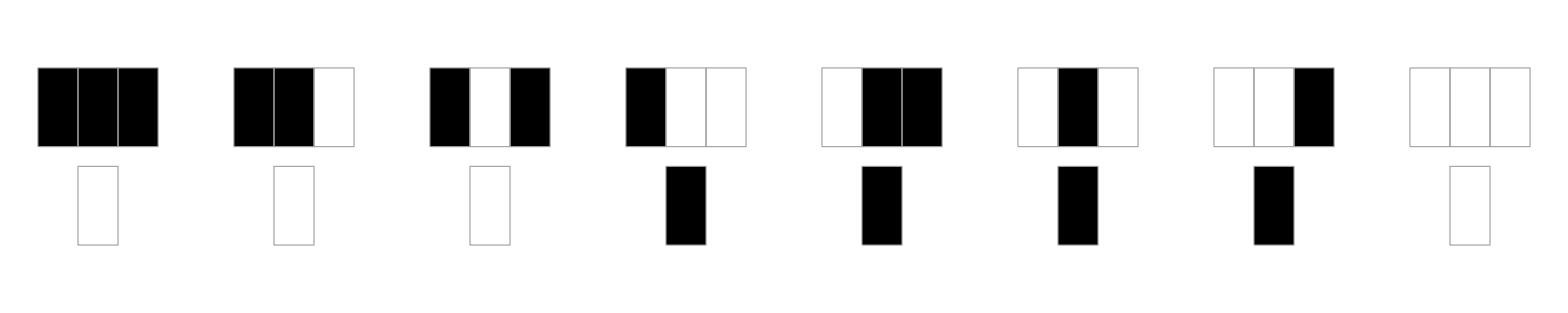

```mathematica
RulePlot[CellularAutomaton["Rule30"], PlotLegends-> "Text"]
```

```mathematica
Note: to investigate the definitions of things, we can use the following:
Inactivate[Needs["GeneralUtilities`"]]
Inactivate[PrintDefinitions[RulePlot]]
```

Note: to investigate the definitions of things, we can use the following:

Needs[GeneralUtilities`]

PrintDefinitions[RulePlot]

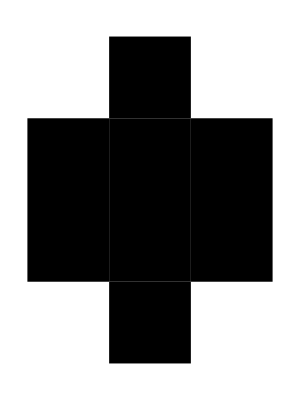

```mathematica
Graphics[{Rectangle[{1,3}], Rectangle[{1,2}], Rectangle[{1,1}], Rectangle[{1,0}], Rectangle[{0,2}], Rectangle[{0,1}],Rectangle[{2,1}], Rectangle[{2,2}]}]
```

```mathematica
{{Null, Rectangle[{,#2}], □, Null}, {□, □, □, □}, {□, □, □, □}, {Null, □, □, Null}}
```

{{Null,Rectangle[{#0,#2}],□,Null},{□,□,□,□},{□,□,□,□},{Null,□,□,Null}}

```mathematica
Manipulate[Graphics[Table[If[ContainsAll[{1,n},{i,j}], Null, Style[Rectangle[{i,j}], RGBColor[(i-1)/(n-1),(j-1)/(n-1),0.5]]], {i, n}, {j,n}]], {n,3,8, 1}]
```